```mathematica
Get[StringJoin[NotebookDirectory[],"PlaneCurvePlot.wl"]]
```

### Tangent

```mathematica
PlaneCurvePlot[{t,Sin[t]},{t,0,6},{1.5,4.1,5.1},TangentLineLength->20,PlotRange->{{-1,7},{-2,2}}]
```

-Graphics-

(* Serpentine *)

```mathematica
PlaneCurvePlot[{t,(3^2 t)/(2^2+t^2)},{t,-5,5},{-1,1.9},TangentLineLength->4]
```

-Graphics-

(* Deltoid *)

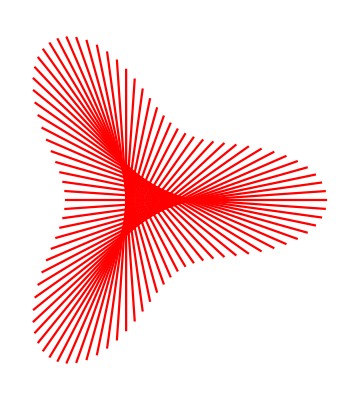

```mathematica
PlaneCurvePlot[{(2 Cos[t])/3+1/3 Cos[2 t],(2 Sin[t])/3-1/3 Sin[2 t]},{t,0,2 π,(2 π)/46},TangentLineLength->5,PlotCurve->False,PlotDot->False,Axes->False]
```

(* cycloid *)

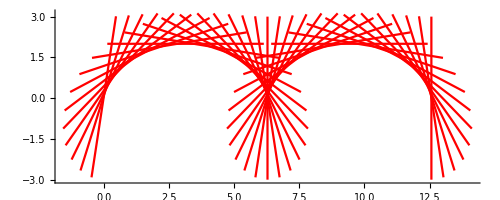

```mathematica
PlaneCurvePlot[{t-Sin[t],1-Cos[t]},{t,0,4 π,.31415},TangentLineLength->6,PlotCurve->False,PlotDot->False]
```

(* epitrochoid type curve *)

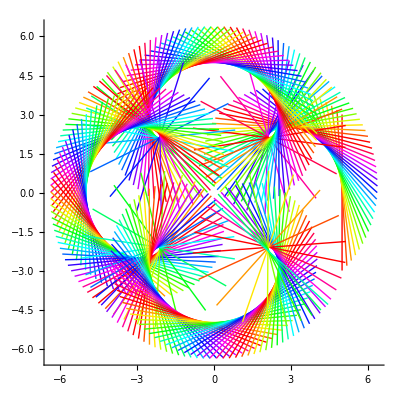

```mathematica
PlaneCurvePlot[{Cos[t]+Cos[t/5] 4,Sin[t]+Sin[t/5] 4},{t,0,9 π,.1},TangentLineLength->6,PlotDot->False,PlotCurve->False,TangentLineStyle->Table[{Hue[i]},{i,0,1,.05}]]
```

(* Tangent crawl *)

```mathematica
PlaneCurvePlot[{t,Cos[t]* Sin[t]+t},{t,-5,10},Range[3,5,0.05],TangentLineLength->6,PlotDot->False,PlotRange->{{-6,11},{-6,11}}]
```

-Graphics-

(* paint splash by tangent *)

```mathematica
PlaneCurvePlot[{t,2 Cos[t]+t},{t,-5,10,.1},TangentLineLength->60,PlotDot->False,PlotRange->{{-6,11},{-6,11}},TangentLineStyle->Table[Hue[i],{i,0,1,.02}]]
```

-Graphics-